Created by: markus on 07-06-2018 14:31:16

### Categorization

Symbol

UpSetChart

UpSetChart`

UpSetChart

Synonyms

Venn Diagram

### Keywords

Venn Diagram

Intersection

Union

### Syntax Templates

Details

Markus van Almsick

Sumner Magruder

Security Details

"   Potential security risk"

# UpSetChart

UpSetChart[<|"set a"→{e_a1,e_a2,...}, "set b"→{e_b1,e_b2,...},...|>] 
makes an upset chart by comparing sets a, b, ... for unique elements

UpSetChart[{{e_i1,e_i2,...},{e_j1,e_j2,...},...}] 
makes an upset chart by comparing elements of set i, j, ... for unique elements

Data elements for UpSetChart can be given in the following forms:

| e_i | a pure value (can be symbolic)

Datasets for UpSetChart can be given in the following forms:

| {{e_i1,ei_2,…},…{e_j1,ej_2,…},…} | list of list of elements with or without wrappers
       | <|"s_i"→{e_i1,…},…,"s_j"→{e_j1,…},…|> | association of keys and lengths

UpSetChart has some of the familiar options as Graphics with the following additions and changes

| "DropEmpty" | True | whether to remove comparisons with no unique elements
       | "Verbose" | Truepaclet:ref/True | whether to output updates as unique elements are calculated 
       | "ColorGradient" | "DeepSeaColors" | what ColorGradient to use as the color function for bars
       | "IntersectionSortBy" | "Name" | bow comparisons are sorted. Valid options are {"Name", "Cardinality"}
       | "SetSortBy" | "Name" | how sets are sorted.Valid options are {"Name","Cardinality"}
       | "TabbedByComparisonsDegreeQ" | True | whether to show all comparisons or tab comparisons by degree (number of sets) in teh comparison.
       | "ImageSize" | Automaticpaclet:ref/Automatic | size of output image

There are 2^n comparisons that need to be made to produce an UpSetCharts. Use of many large sets may take time.

The argument supplied to ColorFunction is the cardinality of the set / comparison

## Tutorials

Related Demonstrations

## Related Links

## See Also

Related Workflows

## More About

Autogenerated

## Examples | More Examples ⊳

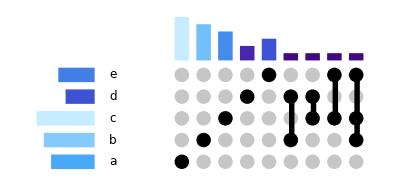

```mathematica
sets=<|
"a"->{7,77,53,95,42,41},
"b"->{51,88,87,67,90,37,96},
"c"->{15,87,99,6,20,87,98,68},
"d"->{46,85,6,90},
"e"->{72,97,15,55,87}
|>;
UpSetChart[sets]
```

## More Examples

### Scope

### Generalizations & Extensions

#### "DynamicUpSetChart"

#### Extending UpSetChart

Components with the data returned from UniqueIntersections or CalcThenSortAndFilter Each component can be rendered individually

```mathematica
<<UpSetChart`Calculations`
```

```mathematica
calc=CalcThenSortAndFilter[sets]
```

<|sets→<|Fruit→{Kiwi,Lemon,Banana,Strawberry,Pear,Apple,Carrot},Green→{Kiwi,Pear,Cucumber,Pickle},Red→{Strawberry,Apple},Tasty→{Kiwi,Pear},Vegetable→{Cucumber,Pickle}|>,comparisons→<|{Fruit}→{Banana,Carrot,Lemon},{Green,Vegetable}→{Cucumber,Pickle},{Red,Fruit}→{Apple,Strawberry},{Green,Tasty,Fruit}→{Kiwi,Pear}|>|>

ComparisonsBarChart

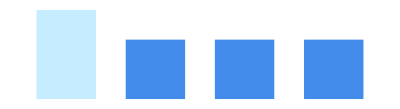

```mathematica
<<UpSetChart`Graphics`ComparisonsBarChart`
ComparisonsBarChart[calc["comparisons"],
 Max[Length/@calc["comparisons"]], Keys@calc["sets"]
]//Graphics[#,ImageSize->Tiny]&
```

IndicatorGrid

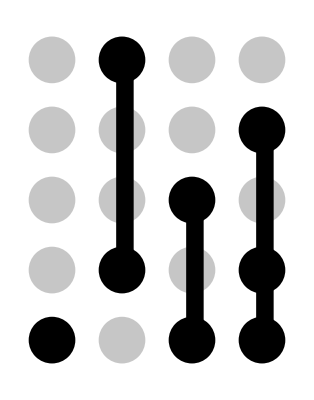

```mathematica
<<UpSetChart`Graphics`IndicatorGrid`
IndicatorGrid[Keys[calc["sets"]],Keys[calc["comparisons"]]]//Graphics[#,ImageSize->Tiny]&
```

SetsBarChart

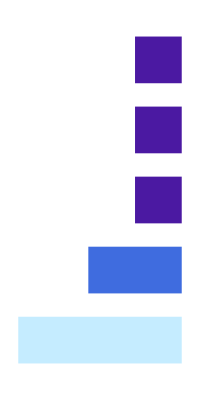

```mathematica
<<UpSetChart`Graphics`SetsBarChart`
SetsBarChart[calc["sets"], Keys[calc["sets"]], Max[Length/@calc["sets"]]]//Graphics[#,ImageSize->Tiny]&
```

SetsLabels

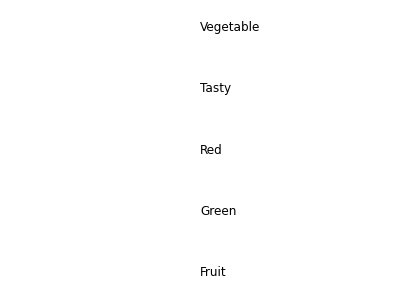

```mathematica
<<UpSetChart`Graphics`SetsLabels`
SetsLabels[ Keys[calc["sets"]]]//Graphics[#,ImageSize->Tiny]&
```

Or returned as a list via

```mathematica
<<UpSetChart`Graphics`Utilities`
```

```mathematica
GraphicComponents[calc["sets"], calc["comparisons"],"IndicatorRadius"->1]
```

{Translate[{{RGBColor[0.772061, 0.92462, 0.998703],Rectangle[{0,2},{7,4}]},{RGBColor[0.24882928571428573, 0.42314085714285715, 0.8732312857142858],Rectangle[{3,5},{7,7}]},{RGBColor[0.29575928571428567, 0.09888902857142857, 0.634997],Rectangle[{5,8},{7,10}]},{RGBColor[0.29575928571428567, 0.09888902857142857, 0.634997],Rectangle[{5,11},{7,13}]},{RGBColor[0.29575928571428567, 0.09888902857142857, 0.634997],Rectangle[{5,14},{7,16}]}},{0,0}],Translate[{{RGBColor[0.772061, 0.92462, 0.998703],Rectangle[Offset[{54,0},{2,0}],Offset[{54,0},{4,3}]]},{RGBColor[0.26669366666666666, 0.550462, 0.926485],Rectangle[Offset[{54,0},{5,0}],Offset[{54,0},{7,2}]]},{RGBColor[0.26669366666666666, 0.550462, 0.926485],Rectangle[Offset[{54,0},{8,0}],Offset[{54,0},{10,2}]]},{RGBColor[0.26669366666666666, 0.550462, 0.926485],Rectangle[Offset[{54,0},{11,0}],Offset[{54,0},{13,2}]]}},{9,17}],Translate[{Text[Fruit,{0,3},{-1,0}],Text[Green,{0,6},{-1,0}],Text[Red,{0,9},{-1,0}],Text[Tasty,{0,12},{-1,0}],Text[Vegetable,{0,15},{-1,0}]},{9,0}],Translate[{{{{GrayLevel[0],Disk[Offset[{54,0},{3,3}],1]},{RGBColor[0.7777777777777778, 0.7777777777777778, 0.7777777777777778],Disk[Offset[{54,0},{6,3}],1]},{GrayLevel[0],Disk[Offset[{54,0},{9,3}],1]},{GrayLevel[0],Disk[Offset[{54,0},{12,3}],1]}},{{RGBColor[0.7777777777777778, 0.7777777777777778, 0.7777777777777778],Disk[Offset[{54,0},{3,6}],1]},{GrayLevel[0],Disk[Offset[{54,0},{6,6}],1]},{RGBColor[0.7777777777777778, 0.7777777777777778, 0.7777777777777778],Disk[Offset[{54,0},{9,6}],1]},{GrayLevel[0],Disk[Offset[{54,0},{12,6}],1]}},{{RGBColor[0.7777777777777778, 0.7777777777777778, 0.7777777777777778],Disk[Offset[{54,0},{3,9}],1]},{RGBColor[0.7777777777777778, 0.7777777777777778, 0.7777777777777778],Disk[Offset[{54,0},{6,9}],1]},{GrayLevel[0],Disk[Offset[{54,0},{9,9}],1]},{RGBColor[0.7777777777777778, 0.7777777777777778, 0.7777777777777778],Disk[Offset[{54,0},{12,9}],1]}},{{RGBColor[0.7777777777777778, 0.7777777777777778, 0.7777777777777778],Disk[Offset[{54,0},{3,12}],1]},{RGBColor[0.7777777777777778, 0.7777777777777778, 0.7777777777777778],Disk[Offset[{54,0},{6,12}],1]},{RGBColor[0.7777777777777778, 0.7777777777777778, 0.7777777777777778],Disk[Offset[{54,0},{9,12}],1]},{GrayLevel[0],Disk[Offset[{54,0},{12,12}],1]}},{{RGBColor[0.7777777777777778, 0.7777777777777778, 0.7777777777777778],Disk[Offset[{54,0},{3,15}],1]},{GrayLevel[0],Disk[Offset[{54,0},{6,15}],1]},{RGBColor[0.7777777777777778, 0.7777777777777778, 0.7777777777777778],Disk[Offset[{54,0},{9,15}],1]},{RGBColor[0.7777777777777778, 0.7777777777777778, 0.7777777777777778],Disk[Offset[{54,0},{12,15}],1]}}},{{GrayLevel[0],Rectangle[Offset[{54,0},{11/4,3}],Offset[{54,0},{7/2,3}]]},{GrayLevel[0],Rectangle[Offset[{54,0},{23/4,6}],Offset[{54,0},{13/2,15}]]},{GrayLevel[0],Rectangle[Offset[{54,0},{35/4,3}],Offset[{54,0},{19/2,9}]]},{GrayLevel[0],Rectangle[Offset[{54,0},{47/4,3}],Offset[{54,0},{25/2,12}]]}}},{9,0}]}

#### More control over UpSetChart

While realigning the four main components above allows for the most control over UpSetChart, several spacing parameters are accessible via UpSetGraphics

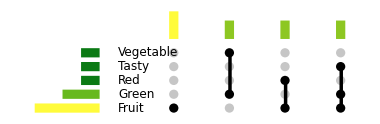

```mathematica
UpSetGraphics[
	calc["sets"], 
	calc["comparisons"],
	"ColorGradient"->"AvocadoColors",
	"ComponentSpacing"->{1,1},
	"IndicatorRadius"->0.5,
	"IndicatorSpacing"->{5,1/2}
]
```

#### Utilities

UpSetChart utilities has several useful properties for ensuring data is safe to be used

```mathematica
<<UpSetChart`Utilities`
```

```mathematica
EnsureLabeledSets[{{1,2,3},{2,3,4,4,4}}]
```

<|a→{1,2,3},b→{2,3,4}|>

```mathematica
sets={{1,2,3},{2,3,4,4,4}};
ListOfListsQ[sets]
LabeledSetsQ[sets]
LabeledSetsQ[EnsureLabeledSets[sets]]
```

True

False

True

### Options

#### "DropEmpty"

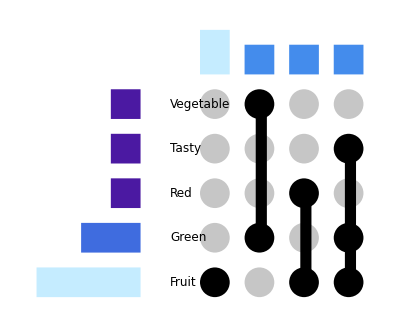

```mathematica
UpSetChart[sets,"DropEmpty"->True]
```

#### "IntersectionSortBy"

```mathematica
<<UpSetChart`TestData`
sets=DummyData[3]
(*<|
"Red"->{"Strawberry","Apple"},"Green"->{"Kiwi","Pear","Cucumber","Pickle"},"Tasty"->{"Kiwi","Pear"},"Fruit"->{"Kiwi","Lemon","Banana","Strawberry","Pear","Apple","Carrot"},"Vegetable"->{"Cucumber","Pickle"}
|>*)
```

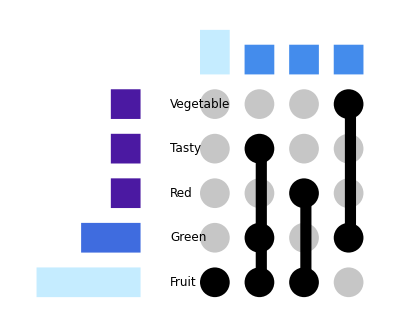

```mathematica
UpSetChart[sets,"IntersectionSortBy"->"Cardinality"]
```

#### "SetSortBy"

```mathematica
<<UpSetChart`TestData`
sets=DummyData[3]
(*<|
"Red"->{"Strawberry","Apple"},"Green"->{"Kiwi","Pear","Cucumber","Pickle"},"Tasty"->{"Kiwi","Pear"},"Fruit"->{"Kiwi","Lemon","Banana","Strawberry","Pear","Apple","Carrot"},"Vegetable"->{"Cucumber","Pickle"}
|>*)
```

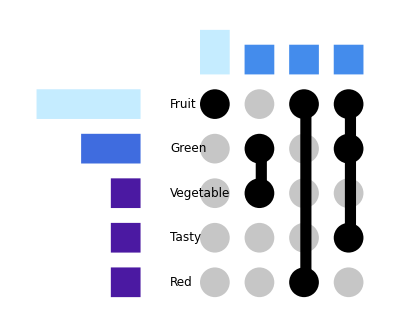

```mathematica
UpSetChart[sets,"SetSortBy"->"Cardinality"]
```

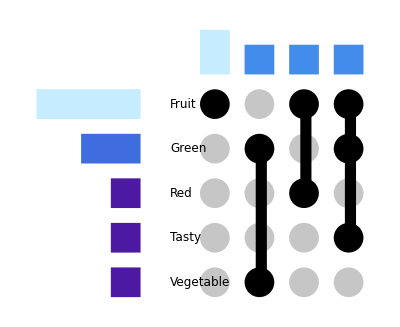

```mathematica
UpSetChart[sets,"SetSortBy"->"Name"]
```

#### "TabbedByComparisonsDegreeQ"

```mathematica
<<UpSetChart`TestData`
sets=DummyData[3]
(*<|
"Red"->{"Strawberry","Apple"},"Green"->{"Kiwi","Pear","Cucumber","Pickle"},"Tasty"->{"Kiwi","Pear"},"Fruit"->{"Kiwi","Lemon","Banana","Strawberry","Pear","Apple","Carrot"},"Vegetable"->{"Cucumber","Pickle"}
|>*)
```

```mathematica
UpSetChart[sets ]
```

-Graphics-

```mathematica
UpSetChart[sets,"TabbedByComparisonsDegreeQ"->True ,"ImageSize"->{Automatic,200}]
```

123

### Applications

### Properties & Relations

#### Use UniqueIntersections to get the unique elements for each comparison (taking into account all sets)

```mathematica
<<UpSetChart`UniqueIntersections`
UniqueIntersections[sets]
```

#### UpSetChart is another way of visualizing venn diagrams

### Possible Issues

Large number of sets can be an issue.

DynamicUpSetChart is very resource intensive.

### Interactive Examples

### Neat Examples

Design Discussion

Application Notes

Test Cases

Function Essay